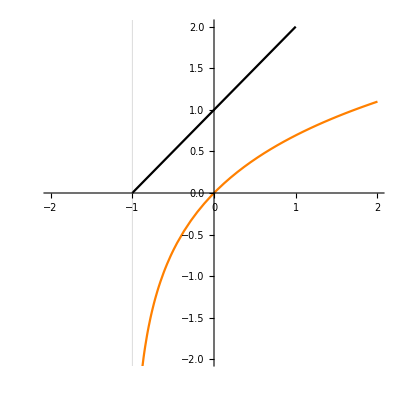

/Users/johnbunce/Dropbox/Matsigenka-Mestizo_project_2014/perception_analysis/xcult_dynamics/figures/ergoplotlab.pdf

```mathematica
(*non-ergotic payoff function*)
m=1;

ergoplot=Show[Plot[x+m,{x,-1,2},PlotRange->{{-2,2},{-2,2}},AspectRatio->1,PlotStyle->Black,GridLines->{{{-1,{CapForm["Butt"],Dashing[0.03],Black}}},{}}],
Plot[Log[x+m],{x,-2,2},PlotStyle->Orange]];

ergoplotlab=GraphicsGrid[
{{ergoplot}},

Spacings->{
{
Scaled[0.5], (*horizontal spacing: before, middle, end of row of figures*)
Scaled[0.5]
},
{
Scaled[0.5], (*vertical spacing: above, middles, bottom of column of figures*)
Scaled[0.5]
}
},

Frame->True,
FrameStyle->Directive[White],

xmv=170;
ymv=-240;

Epilog->{
Inset[Style[OverTilde[w],12, Italic,FontFamily->"Cambria"],{420,-220}],
Inset[Style[OverHat[u],12, Italic,FontFamily->"Cambria"],{230,-30}],
Inset[Style[HoldForm[m=1],12,FontFamily->"Cambria"],{146+xmv,-140+ymv}],
(*Inset[Style[HoldForm[m=2],12,FontFamily->"Cambria"],{140,-140}],*)

Inset[Style[HoldForm[Subscript[OverHat[u],g]=Log[e,OverTilde[w]+m]],12,FontFamily->"Cambria"],{183+xmv,-100+ymv}],
Inset[Style[HoldForm[Subscript[OverHat[u],a]=OverTilde[w]+m],12,FontFamily->"Cambria"],{161+xmv,-60+ymv}],
{AbsoluteThickness[2],Black,Line[{{80+xmv,-60+ymv},{110+xmv,-60+ymv}}]},
{AbsoluteThickness[2],Orange,Line[{{80+xmv,-100+ymv},{110+xmv,-100+ymv}}]}
},
ImageSize->300
](*Graphics Grid*)

(*
Export["C:\\Users\\jabunce\\Dropbox\\Matsigenka-Mestizo_project_2014\\perception_analysis\\xcult_dynamics\\figures\\ergoplotlab.pdf",ergoplotlab,"PDF"]
*)
Export["/Users/johnbunce/Dropbox/Matsigenka-Mestizo_project_2014/perception_analysis/xcult_dynamics/figures/ergoplotlab.pdf",ergoplotlab,"PDF"]
```